# OpenTA1.1

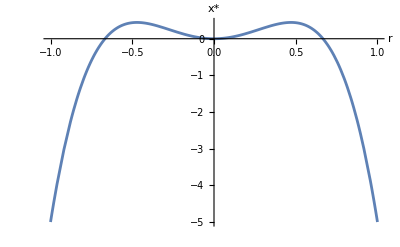

```mathematica
Plot[(4x^3-9x^5)/x, {x,-1,1}, AxesLabel -> {"r", "x*"}]
```

```mathematica
f[x_]:= r*x+4x^3-9x^5
fps=Solve[f[x]==0,x]//Flatten//Simplify
```

{x→0,x→-1/3 √(2-√(4+9 r)),x→1/3 √(2-√(4+9 r)),x→-1/3 √(2+√(4+9 r)),x→1/3 √(2+√(4+9 r))}

```mathematica
D[f[x],x]/.fps[[1]]
D[f[x],x]/.fps[[2]]//Simplify
D[f[x],x]/.fps[[3]]//Simplify
D[f[x],x]/.fps[[4]]//Simplify
D[f[x],x]/.fps[[5]]//Simplify
```

r

4/9 (-4-9 r+2 √(4+9 r))

4/9 (-4-9 r+2 √(4+9 r))

-4/9 (4+9 r+2 √(4+9 r))

-4/9 (4+9 r+2 √(4+9 r))

```mathematica
fps[[5]]
```

x→1/3 √(2+√(4+9 r))

```mathematica
Manipulate[Plot[r*x + 4x^3 - 9x^5,{x,-1,1},AxesLabel -> {"x", "dx/dt"}],{r,-1,1}]
```

```mathematica
p1=Plot[{fps[[1,2]]},{r,-1,0},PlotStyle->{Blue}];
p2=Plot[{fps[[2,2]]},{r,-1,1},PlotStyle->{Dashed,Red}];
p3=Plot[{fps[[3,2]]},{r,-1,1},PlotStyle->{Dashed,Red}];
p4=Plot[{fps[[4,2]]},{r,-1,1},PlotStyle->{Blue}];
p5=Plot[{fps[[5,2]]},{r,-1,1},PlotStyle->{Blue}];
p6=Plot[{fps[[1,2]]},{r,0,1},PlotStyle->{Dashed,Red}];
```

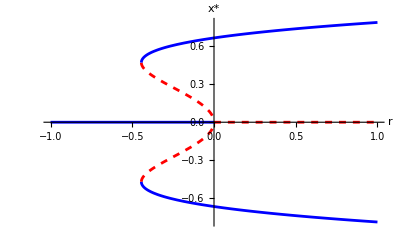

```mathematica
Show[p1, p2, p3, p4, p5, p6, PlotRange -> All, AxesLabel -> {"r", "x*"}]
```

```mathematica
Solve[4/9 (-4-9 r+2 √(4+9 r))==0,r]
```

{{r→-4/9},{r→0}}